```mathematica
(* this is how PCA works in math....*)
(*cv=Eigenvalues[Chop[Covariance[sample]]];
vp=Chop[Eigenvectors[Chop[Covariance[sample]]]];
(* sample is raw, so transpose vp*)
ppc=Chop[sample[[1]].vpᵀ];
kk=Table[If[ppc[[i]]<0,-1,1],{i,Length[ppc]}];
stm=DiagonalMatrix[kk];
tvp=vpᵀ.stm;
(* result is also raw-wised*)
ppc1=Chop[sample.tvp];
Dimensions[ppc1]*)
```

```mathematica
(* build a set of sample*)
s1=RandomVariate[MultinormalDistribution[{1,1},{{0.1,0},{0,0.1}}],100];
s2=RandomVariate[MultinormalDistribution[{-1,-1},{{0.1,0},{0,0.1}}],100];
Dimensions[s2]
```

{100,2}

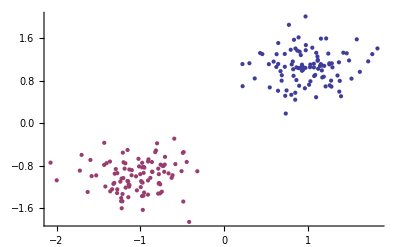

```mathematica
ListPlot[{s1,s2}]
```

```mathematica
sample=Join[s1,s2];
```

```mathematica
pc=PrincipalComponents [sample,Method->"Correlation"];
Dimensions[pc]
```

{10,5}

```mathematica
Mean[pc]
```

{1.11022×10^-16,-4.85723×10^-18,3.52149×10^-17,3.3697×10^-17,9.97466×10^-19}

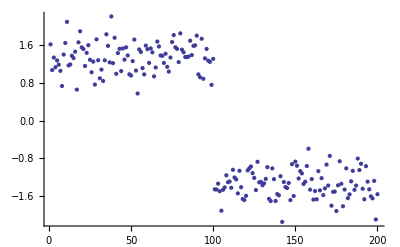

```mathematica
ListPlot[pc[[All,1]]]
(* so not all features separate two classes*)
```

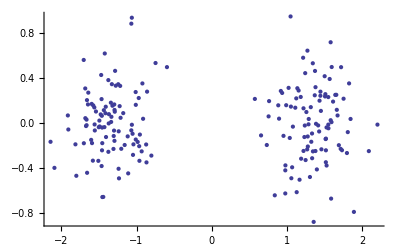

```mathematica
ListPlot[pc]
```

```mathematica
(* try Sw and Sm*)
feature=pc[[All,1]];
```

```mathematica
Total[feature[[;;100]]]
Mean[feature[[101;;]]]
```

134.285

-1.34285

```mathematica
Sw=Covariance[feature[[;;50]]]+Covariance[feature[[51;;]]];
```

```mathematica
m=Mean[feature];
mm={Mean[feature[[;;50]]],Mean[feature[[51;;]]]};
Sb=(mm[[1]]-m)^2+(mm[[2]]-m)^2;
```

```mathematica
Sb/Sw
```

1.07593

```mathematica
Tr[Covariance[pcᵀ]]
```

199.